```mathematica
SetAttributes[unoCardGenerator,HoldAll];
unoCardGenerator[cardLst_]:=Module[
{i,info,number,color,num,step,cardSymbol1,cardSymbol2,cardSymbol3,showLst={}},
For[i=1,i≤Length[cardLst],i++,
info=cardLst[[i,3]];
number=cardLst[[i,2]];
color=cardLst[[i,1]];
cardSymbol1=Text[Style[number,White,Bold,Italic,20],{0.7,7.2}];
cardSymbol2=Text[Style[number,White,Bold,Italic,20],{4.3,0.8}];
cardSymbol3=Text[Style[number,color,Bold,Italic,80],{2.3,4}];
If[number==="skip",
cardSymbol1=Translate[Scale[skipGraphic[White],0.25],{0.8,7.2}];
cardSymbol2=Translate[Scale[skipGraphic[White],0.25],{4.2,0.8}];
cardSymbol3=Translate[Scale[skipGraphic[color],0.9],{2.5,4}];
];
If[number==="reverse",
cardSymbol1=Translate[Scale[reverseGraphic[White],0.25],{0.3,7.5}];
cardSymbol2=Translate[Scale[reverseGraphic[White],0.25],{3.8,1.4}];
cardSymbol3=Translate[Scale[reverseGraphic[color],0.9],{2,4.5}];
];
If[number==="wild",
cardSymbol1=Translate[Scale[wildGraphic,0.2],{-1.6,2.9}];
cardSymbol2=Translate[Scale[wildGraphic,0.2],{1.6,-2.9}];
cardSymbol3=wildGraphic;
];
If[number==="draw2",
cardSymbol1=Text[Style["+2",White,Bold,Italic,20],{0.9,7.2}];
cardSymbol2=Text[Style["+2",White,Bold,Italic,20],{4.1,0.8}];
cardSymbol3=Translate[drawTwoGraphic[color],{1.1,2.5}];
];
num=Mod[i,7]/.Dispatch[0->7];
step=(i-num)/7;
If[info==="selected",
AppendTo[showLst,Translate[{{FaceForm[color],Rectangle[{0.3,0.3},{4.7,7.7},RoundingRadius->0.2]},{White,Rotate[Disk[{2.5,4},{3.5,1.9}],60Degree]},{EdgeForm[{Thin,Black}],FaceForm[Transparent],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},cardSymbol1,cardSymbol2,cardSymbol3,{EdgeForm[{Thickness[0.005],Green}],FaceForm[Transparent],Rectangle[{-0.1,-0.1},{5.1,8.1},RoundingRadius->0.5]}},{6(num-1),-9step}]],
AppendTo[showLst,Translate[{{FaceForm[color],Rectangle[{0.3,0.3},{4.7,7.7},RoundingRadius->0.2]},{White,Rotate[Disk[{2.5,4},{3.5,1.9}],60Degree]},{EdgeForm[{Thin,Black}],FaceForm[Transparent],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},cardSymbol1,cardSymbol2,cardSymbol3},{6(num-1),-9step}]]
];
];
num=num+1;
step=(i-num)/7;
While[num≤7&&step≤1,
AppendTo[showLst,Translate[{FaceForm[Transparent],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},{6(num-1),-9step}]];
num++
];
Return[Graphics[showLst,ImageSize->Full]]
]
```

```mathematica
unoCardGenerator[{{Green,"draw2","okay"}}]
```

-Graphics-

```mathematica
SetAttributes[placeCard,HoldAll];
placeCard[cardLst_,openingCardLst_]:=Module[
{i},
For[i=1,i≤Length[cardLst],i++,
If[cardLst[[i,3]]==="selected",
AppendTo[openingCardLst,cardLst[[i]]];
cardLst=Delete[cardLst,i]
];
];
]
```

```mathematica
cardLst1={{Green,3},{Blue,"skip"},{Red,"reverse"},{Black,"wild"},{Green,3},{Blue,"skip"},{Red,"reverse"},{Black,"wild"},{Green,3},{Blue,"skip"},{Red,"reverse"},{Black,"wild"},{Green,3},{Blue,"skip"},{Red,"reverse"},{Black,"wild"}};
```

```mathematica
placeCard[cardLst1,2]
```

{{RGBColor[0, 1, 0],3},{RGBColor[1, 0, 0],reverse},{GrayLevel[0],wild},{RGBColor[0, 1, 0],3},{RGBColor[0, 0, 1],skip},{RGBColor[1, 0, 0],reverse},{GrayLevel[0],wild},{RGBColor[0, 1, 0],3},{RGBColor[0, 0, 1],skip},{RGBColor[1, 0, 0],reverse},{GrayLevel[0],wild},{RGBColor[0, 1, 0],3},{RGBColor[0, 0, 1],skip},{RGBColor[1, 0, 0],reverse},{GrayLevel[0],wild}}

```mathematica
displayImage[modelInfo_]:=unoCardGenerator[modelInfo]
```

```mathematica
modelInfo1={{Green,3,"okay"},{Blue,"skip","okay"},{Red,"reverse","okay"},{Black,"wild","selected"},{Green,3,"okay"},{Blue,"skip","okay"},{Red,"reverse","okay"},{Black,"wild","okay"},{Green,3,"okay"},{Blue,"skip","okay"},{Red,"reverse","okay"},{Black,"wild","okay"},{Green,3,"okay"},{Blue,"skip","okay"},{Red,"reverse","okay"},{Black,"wild","selected"}};
```

```mathematica
modelInfo1[[1,3]]
```

okay

```mathematica
placeCard[modelInfo1]
```

```mathematica
displayImage[modelInfo1]
```

-Graphics-

```mathematica
modelInfo1={{RGBColor[0, 1, 0],3,"okay"},{RGBColor[0, 0, 1],"skip","okay"},{RGBColor[1, 0, 0],"reverse","okay"},{GrayLevel[0],"wild","okay"},{RGBColor[0, 1, 0],3,"okay"},{RGBColor[0, 0, 1],"skip","okay"},{RGBColor[1, 0, 0],"reverse","okay"},{GrayLevel[0],"wild","okay"},{RGBColor[0, 1, 0],3,"okay"},{RGBColor[0, 0, 1],"skip","okay"},{RGBColor[1, 0, 0],"reverse","okay"},{GrayLevel[0],"wild","okay"},{RGBColor[0, 1, 0],3,"okay"},{RGBColor[0, 0, 1],"skip","okay"},{RGBColor[1, 0, 0],"reverse","okay"},{GrayLevel[0],"wild","okay"}};
```

```mathematica
selectedCard[modelInfo1,{40,5}]
```

{{RGBColor[0, 1, 0],3,selected},{RGBColor[0, 0, 1],skip,okay},{RGBColor[1, 0, 0],reverse,okay},{GrayLevel[0],wild,okay},{RGBColor[0, 1, 0],3,okay},{RGBColor[0, 0, 1],skip,okay},{RGBColor[1, 0, 0],reverse,selected},{GrayLevel[0],wild,okay},{RGBColor[0, 1, 0],3,okay},{RGBColor[0, 0, 1],skip,okay},{RGBColor[1, 0, 0],reverse,okay},{GrayLevel[0],wild,okay},{RGBColor[0, 1, 0],3,okay},{RGBColor[0, 0, 1],skip,okay},{RGBColor[1, 0, 0],reverse,okay},{GrayLevel[0],wild,okay}}

```mathematica
SetAttributes[selectedCard,HoldFirst];
selectedCard[cardLst_,clicked_]:=Module[
{},
Table[{
If[
Abs[clicked[[1]]-cardCenters[cardLst][[i,1]]]≤2.5&& Abs[clicked[[2]]-cardCenters[cardLst][[i,2]]]≤4,
cardLst[[i,3]]="selected"
]},{i,1,Length[cardLst],1}
];
Return[cardLst]
]
```

```mathematica
cardCenters[cardLst_]:=Module[
{i=1,num,step,centerLst={}},
While[i≤Length[cardLst],
num=Mod[i,7]/.Dispatch[0->7];
step=(i-num)/7;
AppendTo[centerLst,{2.5+6(num-1),4+-9(step)}];
i++
];
Return[centerLst]
]
```

```mathematica
cardCenters[cardLst1]
```

{{2.5,4},{8.5,4},{14.5,4},{20.5,4},{26.5,4},{32.5,4},{38.5,4},{2.5,-5},{8.5,-5},{14.5,-5},{20.5,-5},{26.5,-5},{32.5,-5},{38.5,-5},{2.5,-14},{8.5,-14}}

```mathematica
Mod[2,7]/.Dispatch[0->7]
```

2

```mathematica
reverseGraphic[color_]:=Module[
{reverseSymbol,otherReverseSymbol},
reverseSymbol={{FaceForm[color],Disk[{0,0},1,{0,Pi}]},{FaceForm[color],Rectangle[{0,0},{1.1,1}]},{FaceForm[color],Triangle[{{1,1.5},{2,0.5},{1,-0.5}}]}};
otherReverseSymbol=Translate[Rotate[{reverseSymbol},180Degree],{0,-1.9}];
Return[{Rotate[reverseSymbol,45Degree],Rotate[otherReverseSymbol,45Degree]}]
]
```

```mathematica
wildGraphic={Rotate[{White,Disk[{2.5,4},{3.5,1.9}]},60Degree],Rotate[{Blue,Disk[{2.5,4},{3.3,1.7},{-0.408Pi,0.09Pi}]},60Degree,{2.5,4}],Rotate[{Red,Disk[{2.5,4},{3.3,1.7},{0.09Pi,0.592Pi}]},60Degree,{2.5,4}],Rotate[{Yellow,Disk[{2.5,4},{3.3,1.7},{0.592Pi,1.09Pi}]},60Degree,{2.5,4}],Rotate[{Green,Disk[{2.5,4},{3.3,1.7},{1.09Pi,1.592Pi}]},60Degree,{2.5,4}]};
```

```mathematica
skipGraphic[color_]:={{color,Annulus[{0,0},{1.1,1.5}]},{color,Polygon[{{-1,-1},{-0.6,-1.2},{1,1},{0.6,1.2}}]}}
```

```mathematica
drawTwoGraphic[color_]:={color,EdgeForm[{Thick,White}],Rectangle[{1,1},{2.25,3},RoundingRadius->0.1],Rectangle[{0.5,0},{1.75,2},RoundingRadius->0.1]}
```

```mathematica
playerSwitch[]
```

playerSwitch[]

```mathematica
lalist={{{{1,1},1},{{3,3},1},{{5,5},1}},{{{1,5},1},{{3,3},1},{{5,1},1}}};
```

{{{{1,1},1},{{3,3},1},{{5,5},1}},{{{1,5},1},{{3,3},1},{{5,1},1}}}

```mathematica
Graphics3D[{{Texture[Graphics[{Translate[{{FaceForm[RGBColor[0, 1, 0]],Rectangle[{0.3,0.3},{4.7,7.7},RoundingRadius->0.2]},{GrayLevel[1],Disk[{2.5,4},{3.5,1.9}]},{EdgeForm[{Thickness[Tiny],GrayLevel[0]}],FaceForm[GrayLevel[0, 0]],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},Text["+2",{0.9,7.2}],Text["+2",{4.1,0.8}],Translate[{RGBColor[0, 1, 0],EdgeForm[{Thickness[Large],GrayLevel[1]}],Rectangle[{1,1},{2.25,3},RoundingRadius->0.1],Rectangle[{0.5,0},{1.75,2},RoundingRadius->0.1]},{1.1,2.5}]},{0,0}],Translate[{FaceForm[GrayLevel[0, 0]],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},{6,0}],Translate[{FaceForm[GrayLevel[0, 0]],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},{12,0}],Translate[{FaceForm[GrayLevel[0, 0]],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},{18,0}],Translate[{FaceForm[GrayLevel[0, 0]],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},{24,0}],Translate[{FaceForm[GrayLevel[0, 0]],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},{30,0}],Translate[{FaceForm[GrayLevel[0, 0]],Rectangle[{0,0},{5,8},RoundingRadius->0.4]},{36,0}]}]],{Black,Polygon[{{-1,-0.25,-1},{1,-0.25,-1},{1,0.25,-1},{-1,0.25,-1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}},{Texture[Graphics[{Opacity[0.5],Red,Disk@@@lalist[[1]]},Frame->True]],Polygon[{{-1,-1,1},{1,-1,1},{1,1,1},{-1,1,1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}},Lighting->"Neutral",ViewPoint->Front]
```

-Graphics3D-

```mathematica
Refle
```

```mathematica
Graphics3D[{{Texture[Graphics[{Opacity[0.5],Blue,Disk@@@lalist[[2]]},Frame->True]],Polygon[{{-1,-1,-1},{-1,-1,1},{1,-1,1},{1,-1,-1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},{Texture[Graphics[{Opacity[0.5],Red,Disk@@@lalist[[1]]},Frame->True]],Polygon[{{-1,-1,1},{1,-1,1},{1,1,1},{-1,1,1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]}},Lighting->"Neutral",ViewPoint->Front]
```

-Graphics3D-

```mathematica
symbolToPolygon[symbol_,dimension_:"2D"]:=Module[{pol,poly,index,pos,minmax,diffs,poly2D},pol=(Cases[ImportString[ExportString[symbol,"PDF"],"PDF"],_FilledCurve,∞][[1,2]]);
poly=pol[[1]];
index=2;
While[index≤Length[pol],pos=Position[poly,Nearest[poly,pol[[index,1]]][[1]]][[1,1]];
poly=Join[Take[poly,pos],Reverse[pol[[index]]],Drop[poly,pos-1]];
index++];
minmax=MinMax/@Transpose[poly];
diffs=#[[2]]-#[[1]]&/@minmax;
poly2D=(#-Mean/@minmax)/Max[diffs]&/@poly;
If[dimension==="2D",Polygon[poly2D],Polygon[Append[#,1]&/@poly2D]]]
```

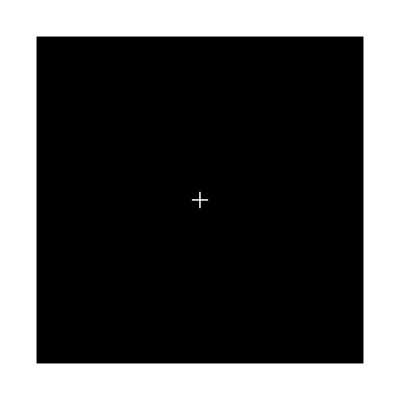

```mathematica
Graphics[{{Black,Rectangle[{-10,-10},{10,10}]},{White,symbolToPolygon["+1"]}}]
```

```mathematica
symbolToPolygon["1+"]
```

Polygon[…]

```mathematica
NotebookDirectory[SetDirectory[]]
```

NotebookDirectory[C:\Users\nkh06531]

```mathematica
Import["https://d.newsweek.com/en/full/520858/supermoon-moon-smartphone-photo-picture.jpg"]
```

-Graphics-

```mathematica
Show[Graphics[{Green,Rectangle[{-100,-100},{600,900}]}],-Graphics-,Axes->True]
```

-Graphics-